```mathematica
Lx := 2
Ly := 2
```

```mathematica
En[n_, m_] := Pi^2 * (n^2 / Lx^2 + m^2 / Ly^2)
```

```mathematica
psi[n_, m_, x_, y_] := 2 / Sqrt[Lx Ly] Cos[Pi n / Lx x] Cos[Pi m / Ly y]
```

```mathematica
G[x_, y_, xs_, ys_, EE_, maxnm_] := Sum[psi[n, m, x, y] psi[n, m, xs, ys] / (En[n, m] - EE),{n,0,maxnm},{m,0,maxnm}]
```

```mathematica
N[Norm[G[0, 0, 0, 0, 2]^2]]
```

21.3787

```mathematica
x0 := Lx / 2
y0 := 0
```

```mathematica
N[Norm[G[x0, y0, x0, y0, 10, 300]]^2]
```

177.332

```mathematica
N[Norm[G[x0, y0, x0, y0, 10, 1000]]^2]
```

167.268

```mathematica
N[Norm[G[x0, y0, x0, y0, 10, 2000]]^2]
```

161.609

```mathematica
N[Norm[G[x0, y0, x0, y0, 15, 1000]]^2]
```

2.32049

```mathematica
N[Norm[G[0, 0, x0, y0, 15, 1000]]^2]
```

0.0709968

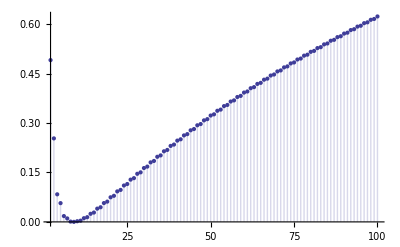

```mathematica
DiscretePlot[Norm[G[x0, y0, x0, y0, 15, maxnm]^2], {maxnm, 2, 100}]
```

```mathematica
q
```

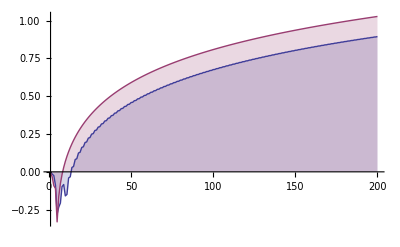

```mathematica
DiscretePlot[{
Re[G[x0, y0, x0, y0, 3]],
Re[GG[3]]}
, {maxnm, 1, 200}]
```

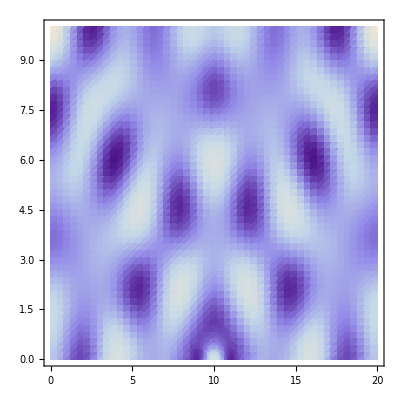

```mathematica
DensityPlot[Re[G[x, y, x0, y0, 3]],{x,0.0,Lx},{y,0.0,Ly}, ImageSize->Full, PlotPoints->50]
```

```mathematica
N[Sqrt[I]]
```

0.707107+0.707107 ⅈ